```mathematica
BeginPackage["PolygonPlotMarkers`"];

ClearAll[PolygonMarker];

Begin["`Private`"];

ClearAll[ centroidAndScale];
 centroidAndScale[coords:{{_?NumericQ,_?NumericQ}..}]:=
With[{
x=coords⟦All,1⟧,y=coords⟦All,2⟧,
i=Range@Length[coords]
},
With[{
xi=x⟦i⟧,yi=y⟦i⟧,
j=Mod[i+1,Length[coords],1]
},
With[{
xj=x⟦j⟧,yj=y⟦j⟧
},
With[{
area=1/2(xi.yj-xj.yi),
factor=xi yj-xj yi
},
With[{
centroid=1/(6 area){(xi+xj).factor,(yi+yj).factor}
},
Transpose[{x,y}-centroid]/Sqrt@Abs[area]
]
]
]
]
];

ClearAll[ngon];
ngon[n_Integer/;n≥3,phase_?NumericQ]:=
 centroidAndScale@Table[
{Sin[2Pi k/n+phase],Cos[2Pi k/n+phase]},
{k,0,n-1}
];

ClearAll[coords];
coords["UpTriangle"]=ngon[3,0];
coords["DownTriangle"]=ngon[3,Pi/3];
coords["LeftTriangle"]=ngon[3,Pi/6];
coords["RightTriangle"]=ngon[3,-Pi/6];
coords["DiagonalSquare"|"Diamond"]=ngon[4,0];
coords["Square"]=ngon[4,Pi/4];
coords["Pentagon"]=ngon[5,0];
coords["FivePointedStar"]={
{0,Root[1296-4500 #1^4+3125 #1^8&,4,0]},
{Root[1-900 #1^4+162000 #1^8&,3,0],Root[1-22500 #1^4+4050000 #1^8&,4,0]},
{Root[81-1800 #1^4+2000 #1^8&,4,0],Root[81-9000 #1^4+50000 #1^8&,3,0]},
{Root[1-1800 #1^4+162000 #1^8&,4,0],Root[1-9000 #1^4+4050000 #1^8&,2,0]},
{Root[81-900 #1^4+2000 #1^8&,3,0],Root[81-22500 #1^4+50000 #1^8&,1,0]},
{0,Root[16-4500 #1^4+253125 #1^8&,1,0]},
{Root[81-900 #1^4+2000 #1^8&,2,0],Root[81-22500 #1^4+50000 #1^8&,1,0]},
{Root[1-1800 #1^4+162000 #1^8&,1,0],Root[1-9000 #1^4+4050000 #1^8&,2,0]},
{Root[81-1800 #1^4+2000 #1^8&,1,0],Root[81-9000 #1^4+50000 #1^8&,3,0]},
{Root[1-900 #1^4+162000 #1^8&,2,0],Root[1-22500 #1^4+4050000 #1^8&,4,0]}
};
coords["Hexagon"]=ngon[6,0];
coords["SixPointedStar"]={
{0,Sqrt[2/3]},{1/(2 Sqrt[6]),1/(2 Sqrt[2])},
{1/Sqrt[2],1/Sqrt[6]},{1/Sqrt[6],0},{1/Sqrt[2],-(1/Sqrt[6])},
{1/(2 Sqrt[6]),-1/(2 Sqrt[2])},{0,-Sqrt[2/3]},
{-1/(2 Sqrt[6]),-1/(2 Sqrt[2])},{-(1/Sqrt[2]),-(1/Sqrt[6])},
{-(1/Sqrt[6]),0},{-(1/Sqrt[2]),1/Sqrt[6]},{-1/(2 Sqrt[6]),1/(2 Sqrt[2])}
};
coords["SixfoldPinwheel"]={
{0,Root[-25+27 #1^4&,2,0]},
{Root[-1+75 #1^4&,2,0],Root[-1+675 #1^4&,2,0]},
{Root[-25+48 #1^4&,2,0],Root[-25+432 #1^4&,2,0]},
{Root[-1+75 #1^4&,2,0],Root[-1+675 #1^4&,1,0]},
{Root[-25+48 #1^4&,2,0],Root[-25+432 #1^4&,1,0]},
{0,Root[-16+675 #1^4&,1,0]},{0,Root[-25+27 #1^4&,1,0]},
{Root[-1+75 #1^4&,1,0],Root[-1+675 #1^4&,1,0]},
{Root[-25+48 #1^4&,1,0],Root[-25+432 #1^4&,1,0]},
{Root[-1+75 #1^4&,1,0],Root[-1+675 #1^4&,2,0]},
{Root[-25+48 #1^4&,1,0],Root[-25+432 #1^4&,2,0]},
{0,Root[-16+675 #1^4&,2,0]}
};
coords["EightPointedStar"]={
{0,Root[1-16 #1^4+32 #1^8&,4,0]},
{Root[1-2048 #1^4+524288 #1^8&,3,0],Root[1-10240 #1^4+524288 #1^8&,4,0]},
{Root[1-64 #1^4+512 #1^8&,4,0],Root[1-64 #1^4+512 #1^8&,4,0]},
{Root[1-10240 #1^4+524288 #1^8&,4,0],Root[1-2048 #1^4+524288 #1^8&,3,0]},
{Root[1-16 #1^4+32 #1^8&,4,0],0},
{Root[1-10240 #1^4+524288 #1^8&,4,0],Root[1-2048 #1^4+524288 #1^8&,2,0]},
{Root[1-64 #1^4+512 #1^8&,4,0],Root[1-64 #1^4+512 #1^8&,1,0]},
{Root[1-2048 #1^4+524288 #1^8&,3,0],Root[1-10240 #1^4+524288 #1^8&,1,0]},
{0,Root[1-16 #1^4+32 #1^8&,1,0]},
{Root[1-2048 #1^4+524288 #1^8&,2,0],Root[1-10240 #1^4+524288 #1^8&,1,0]},
{Root[1-64 #1^4+512 #1^8&,1,0],Root[1-64 #1^4+512 #1^8&,1,0]},
{Root[1-10240 #1^4+524288 #1^8&,1,0],Root[1-2048 #1^4+524288 #1^8&,2,0]},
{Root[1-16 #1^4+32 #1^8&,1,0],0},
{Root[1-10240 #1^4+524288 #1^8&,1,0],Root[1-2048 #1^4+524288 #1^8&,3,0]},
{Root[1-64 #1^4+512 #1^8&,1,0],Root[1-64 #1^4+512 #1^8&,4,0]},
{Root[1-2048 #1^4+524288 #1^8&,2,0],Root[1-10240 #1^4+524288 #1^8&,4,0]}
};
coords["EightfoldPinwheel"]={
{0,Root[-1+2 #1^4&,2,0]},
{Root[-1+128 #1^4&,2,0],Root[-1+128 #1^4&,2,0]},
{Root[-1+8 #1^4&,2,0],Root[-1+8 #1^4&,2,0]},
{Root[-1+32 #1^4&,2,0],0},
{Root[-1+2 #1^4&,2,0],0},
{Root[-1+128 #1^4&,2,0],Root[-1+128 #1^4&,1,0]},
{Root[-1+8 #1^4&,2,0],Root[-1+8 #1^4&,1,0]},
{0,Root[-1+32 #1^4&,1,0]},
{0,Root[-1+2 #1^4&,1,0]},
{Root[-1+128 #1^4&,1,0],Root[-1+128 #1^4&,1,0]},
{Root[-1+8 #1^4&,1,0],Root[-1+8 #1^4&,1,0]},
{Root[-1+32 #1^4&,1,0],0},
{Root[-1+2 #1^4&,1,0],0},
{Root[-1+128 #1^4&,1,0],Root[-1+128 #1^4&,2,0]},
{Root[-1+8 #1^4&,1,0],Root[-1+8 #1^4&,2,0]},
{0,Root[-1+32 #1^4&,2,0]}
};
coords["Cross"]= centroidAndScale@With[{a=1/6},Join@@NestList[#.{{0,-1},{1,0}}&,{{-a,1},{a,1},{a,a}},3]];
coords["DiagonalCross"]=coords["Cross"].RotationMatrix[Pi/4];

PolygonMarker[name_String,size_?NumericQ,offset:{_?NumericQ,_?NumericQ}:{0,0}]:=
Polygon@Transpose[Transpose[size coords[name]]+offset];
PolygonMarker[name_String,Scaled[size_?NumericQ],offset:{_?NumericQ,_?NumericQ}:{0,0}]:=
Polygon[Scaled[size #,offset]&/@coords[name]];
PolygonMarker[coords:{{_?NumericQ,_?NumericQ}..},size_?NumericQ,offset:{_?NumericQ,_?NumericQ}:{0,0}]:=
Polygon@Transpose[Transpose[size centroidAndScale[coords]]+offset];
PolygonMarker[coords:{{_?NumericQ,_?NumericQ}..},Scaled[size_?NumericQ],offset:{_?NumericQ,_?NumericQ}:{0,0}]:=
Polygon[Scaled[size #,offset]&/@centroidAndScale[coords]];

End[];

EndPackage[];
```

```mathematica
shapes={
"UpTriangle","DownTriangle","LeftTriangle",
"RightTriangle","Cross","DiagonalCross",
"Diamond","Square","Pentagon",
"FivePointedStar","Hexagon","SixPointedStar",
"SixfoldPinwheel","EightPointedStar","EightfoldPinwheel"
};
Graphics[{
FaceForm[Hue@Random[]],EdgeForm@Directive[Black,Thickness[0.03]],
PolygonMarker[#,Scaled[1]]
},ImageSize->40]&/@shapes
```

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,
-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

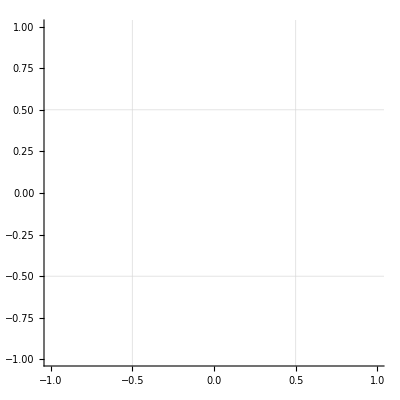

```mathematica
Graphics[{
FaceForm[Blue],EdgeForm@Directive[Red,Thickness[0.02]],
PolygonMarker["DiagonalCross",Scaled[0.2],{0.5,0.5}],
FaceForm[Green],EdgeForm@Directive[Black,Thickness[0.02]],
PolygonMarker["UpTriangle",Scaled[0.2],{-0.5,0.5}],
FaceForm[Yellow],EdgeForm@Directive[Blue,Thickness[0.02]],
PolygonMarker["FivePointedStar",Scaled[0.2],{-0.5,-0.5}],
FaceForm[Black],EdgeForm@Directive[Purple,Thickness[0.02]],
PolygonMarker["SixfoldPinwheel",Scaled[0.2],{0.5,-0.5}]
},Axes->True,PlotRange->{{-1,1},{-1,1}},GridLines->{{-0.5,0.5},{-0.5,0.5}}
]
```

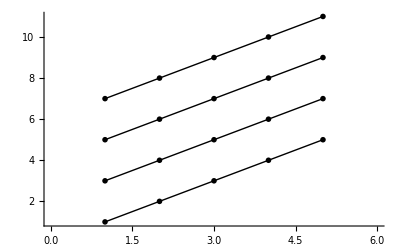

```mathematica
ListPlot[
ConstantArray[Range[5],4]+Range[0,6,2],
PlotStyle->Black,Joined->True,
PlotMarkers->{
Graphics[{FaceForm[Red],EdgeForm[Red],PolygonMarker["FivePointedStar",Scaled[0.05]]}],
Graphics[{FaceForm[None],EdgeForm[Green],PolygonMarker["UpTriangle",Scaled[0.05]]}],
Graphics[{FaceForm[Blue],EdgeForm[Blue],PolygonMarker["Square",Scaled[0.05]]}],
Graphics[{FaceForm[None],EdgeForm[Black],PolygonMarker["DiagonalCross",Scaled[0.04]]}]
},
PlotRange->{{0,6},All}
]
```